Copy of everything from treeDecomposition.m

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Bulatov`common`"];

(* map vertices to indices in adjacency matrix and back *)
(* Needs global V, initialized as V=VertexList[g]; *)
vert2idx[verts_List]:=Flatten[Position[V,Alternatives@@verts]];
idx2vert[idx_List]:=V[[idx]];

(* gets all pairs of bags that intersect *)
intersectingPairs[bags_List]:=Module[{cands,result},
	cands=Outer[List,bags,bags,1]//fl1;
	Select[cands,#[[1]]!=#[[2]]&&!disjoint[#[[1]],#[[2]]]&&OrderedQ[#]&]
];


(* sorts list given list of partial orders, and give first result
partialSortFirst[{a,b,c},{1,1,2}] means a,b are tied for first position, c is in second
 *)
(* partialSortFirst[{1,2,3},{1,1,1},{1,1,2}] gives 1,2 *)
partialSortFirst[items_,orders__]:=(
	ordList=Transpose[{orders}];
	Assert[Length[items]==Length[ordList]];
	best=First@Sort@ordList;
	poses=Position[ordList,_?(#==best&)];
	Sort[Extract[items,poses]]//First
)

(* Get neighborhood of given vertex set. Vertices in the set not included. *)
(* todo: rename to getAdjacent *)
getAdjacent[{}]:=V;
getAdjacent[v_List]:=( 
	vArr=SparseArray[vert2idx[v]->ConstantArray[1,|v|],|V|];
	idx2vert[Cases[ArrayRules[(adjMat.vArr)(1-vArr)],HoldPattern[{x_}->_?Positive]->x]]
);
getAdjacent[v_Integer]:=getAdjacent[{v}];


(* maximum spanning tree *)
spanningBagTree[bags_]:=Module[{jtree,edgeCandidates,bestEdge,lens},
(* return all possible edges, ie, ones that don't create a cycle in current jtree graph *)
	acyclicEdges[ed_]:=Select[ed,AcyclicGraphQ[Graph[UndirectedEdge@@@(jtree∼{#})]]&];

	(* For a given set of junction tree edges, returns one with largest intersection *) 
findHeaviestEdge[ed_]:=(
		lens=|#[[1]]∩#[[2]]|&/@ed;
		If[lens=={},{},ed[[Last@Ordering@lens]]]
	);

	(* grow the tree greedily by one edge, don't introduce cycles *)
	growTree[]:=(
		bestEdge=findHeaviestEdge[edgeCandidates];
		jtree=jtree∼{bestEdge};
		edgeCandidates=edgeCandidates∖{bestEdge};
		edgeCandidates=acyclicEdges[edgeCandidates];
	);
	edgeCandidates=intersectingPairs[bags];
	jtree={};
	While[edgeCandidates!={},growTree[]];
	Sort[jtree]
];

(* returns True if bag is contained inside any other bag in bags *)
isBagRedundant[bag_]:=anyTrue[b∈bags,(b!=bag)∧(bag⊂b)];

(* Produce list of bags, and pairs of adjacent bags that form a junction tree *)
treeDecomposition[gr_Graph]:=(
	g=gr;
	V=VertexList[g];
	adjMat=AdjacencyMatrix[g];
	elimed={}; (* list of nodes that have been eliminated *)
	bags={}; (* junction tree bags, like {1,2,3}, {2,3,4} *)
	tieBreaker=V;
	While[|elimed|<|V|,minFillEliminate[]];bags=Sort[Select[bags,Not[isBagRedundant[#]]&]];jedges=spanningBagTree[bags];
	{bags,jedges}

);

(* connected components of graph restricted to vertex set *)
connComps[v_]:=ConnectedComponents[Subgraph[g,v]];

(* Eliminate single vertex. Globals: elimed, V, bags *)
elimVertex[v_]:=( 
	Assert[!(v∈elimed),"Duplicate elimination"];

	comps=connComps[V∖elimed];
(* componet containing vertex to be eliminated *)
	ourComp=Select[comps,v∈#&]//First;
	boundary=getAdjacent[ourComp];
	AppendTo[bags,boundary∪{v}];
	AppendTo[elimed,v];
);

(* returns negative number of edges in bag created for each member of verts *)
(* todo: once we have tests, return number of fill edges instead *)
getFillValues[{}]:={};
getFillValues[verts_List]:=( 
	Assert[ValueQ[elimed]];
	If[elimed=={},Return[ConstantArray[0,|verts|]]];
	elimArr=SparseArray[vert2idx[elimed]->ConstantArray[1,|elimed|],|V|];
	getFillSingleVert[v_]:=( 
		vArr=SparseArray[vert2idx[{v}]->1,|V|];
		touchArr=adjMat.vArr;
(* all vertices adjacent to elimination candidate + elimination candidate *)
		cliqueArr=elimArr touchArr+vArr;
(* number of undirected edges in graph restricted to cliqueArr *) 
		numEdges=cliqueArr.adjMat.cliqueArr/2;
-numEdges
	);
	getFillSingleVert/@verts
);

(* Single step of min-fill elimination, Globals: elimed, V, tieBreaker *)
minFillEliminate[]:=( 
	frontier=getAdjacent[elimed];
	Assert[frontier!={},"Either nothing left to eliminate or graph not connected"];
	fillVals=getFillValues[frontier];
	tieVals=tieBreaker[[frontier]];
	elimVertex[partialSortFirst[frontier,fillVals,tieVals,frontier]]
);

(* checks that "bags/jedges" forms a junction tree of g *)
checkTreeDecomposition[g_,{bags_,jedges_}]:=(
	isok=True;

(* every node must be contained in some bag *)
	existNodes=Union[VertexList[g]];
	coveredNodes=Union[Flatten[bags]];
	prop=(existNodes===coveredNodes);
	If[!prop,Print["checkTreeDecomposition: violates variable preservation for ",existNodes∖coveredNodes];isok=False];

(* every edge should be contained in some bag *)
	existFactors=Union[List@@@EdgeList[g]];
	coveredFactors=Union[Select[existFactors,anyTrue[bag∈bags,#⊂bag]&]];
	prop=(existFactors===coveredFactors);
	If[!prop,Print["checkTreeDecomposition: violates factor preservation for ",existFactors∖coveredFactors];isok=False];

    isSeparator[{i_,j_}]:=|ConnectedComponents[Subgraph[g,V∖(i∩j)]]|>1;
    separatingEdges=Select[jedges,isSeparator[#]&];
	prop=(Union[separatingEdges]===Union[jedges]);
	If[!prop,Print["checkTreeDecomposition: violates running intersection for ",jedges∖separatingEdges];isok=False];

	gg=Graph[bags,UndirectedEdge@@@jedges];
	prop=ConnectedGraphQ[gg];
	If[!prop,Print["checkTreeDecomposition: tree not connected, have following cc sizes ",Length/@ConnectedComponents[gg]];isok=False];

	(* following check can subsume the previous two if we allow Junction Forests *)
	seps=Intersection@@@jedges;
	sepCount[x_]:=Length@Select[seps,x∈#&];
	bagCount[x_]:=Length@Select[bags,x∈#&];
	vars=Union@Flatten@jedges;
	counts=table[x∈vars,bagCount[x]-sepCount[x]];
	failures=Extract[vars,Position[counts,_?(#!=1&)]];
	failures=={};
	If[!prop,Print["checkTreeDecomposition: generalized running intersection violated for ",failures];isok=False];

	(* data structure checks *)
	If[!allTrue[e∈jedges,OrderedQ[e]],Print["checkTreeDecomposition: some edge is not ordered"];isok=False];
	If[!allTrue[e∈bags,OrderedQ[e]],Print["checkTreeDecomposition: some node is not ordered"];isok=False];
	If[!OrderedQ[jedges],Print["checkTreeDecomposition: edges are not ordered"];isok=False];
	If[!OrderedQ[bags],Print["checkTreeDecomposition: nodes are not ordered"];isok=False];
	If[Union[fl1@jedges]!=bags,Print["nodes and edges don't match"];isok=False];

	isok
);

(* gives number of basic operations needed to evaluate given tree decomposition *)
getTreeCost[{nodes_List,edges_List}]:=(
	edgeCost[{a_,b_}]:=2^|a∩b|(2^|a∖b|+2^|b∖a|);
	sum[e∈edges,edgeCost[e]]
);

(* gives tree width (size of largest bag) of given tree decomposition *)
getTreeWidth[{nodes_List,edges_List}]:=(
	bags=fl1[edges];
	Max[Length/@bags]
);

(** Visualization Utils **)
initGraph[g_]:=(
(* initializing graph *)
(*g=CycleGraph[8,VertexShapeFunction->shapeFunc];
g=Graph[{1<->2,2<->3,2<->9,5<->4,3<->4,4<->8,1<->5,5<->6,6<->7,5<->10,10<->7,7<->8,9<->4},VertexShapeFunction->shapeFunc];*)
(* initializing Graphics *)
masterScale=100;
lineThickness=.5;
vertSize=1/2;

vcoords=Thread[VertexList[g]->(VertexCoordinates/.AbsoluteOptions[g,VertexCoordinates])];
(*g=GridGraph[{3,3},VertexShapeFunction->shapeFunc];*)
gg=Graph[EdgeList[g],VertexCoordinates->vcoords,VertexShapeFunction->shapeFunc];
V=VertexList[g];
elimed={};
bags={};

graphPR=getPlotRange[V/.vcoords];
graphPR=correctPR[graphPR,masterScale];
graphIS=-masterScale Subtract@@@graphPR;
graphStyle="DiagramBlack";
colorList=ColorData["Atoms","ColorList"];
{bags,jedges}=treeDecomposition[g]
);

correctPR[pr_,scale_]:={pr[[1]]+{-1/scale,2/scale},pr[[2]]+{-2/scale,1/scale}};
getPlotRange[lst_]:=(
{xs,ys}=Transpose[lst];
(*two extra 1/scale offsets needed for exact match*){{Min[xs]-lineThickness/2,Max[xs]+lineThickness/2+1/masterScale},{Min[ys]-lineThickness/2-1/masterScale,Max[ys]+lineThickness/2}}
);

vertexClick[v_]:=(
Print["eliminating ",v];
elim[v];
);

(* regular ymin-1,xmax+1, and addition 1 pixel for antialiasing *)
makeVertex[{x_,y_},v_]:=(
plotRange=Transpose[{{x,y}-vertSize/2,{x,y}+vertSize/2}];
plotRange=correctPR[plotRange,masterScale];
imageSize=-masterScale Subtract@@@plotRange;
button={Transparent,EdgeForm[Thick],Button[Disk[{x,y},vertSize/2],vertexClick[v]]};
label={Black,Style[Text[v,{x,y}],Bold,14]};
label∼button
);
shapeFunc[{x_,y_},v_,{w_,h_}]:=makeVertex[{x,y},v];

drawBag[bag_List,scale_:masterScale]:=(
bagGraph=Subgraph[g,bag,VertexCoordinates->vcoords,GraphStyle->graphStyle];
tileEnds=Select[Outer[List,bag,bag]//fl1,#⟦1⟧≤#⟦2⟧&];
tiles=FindShortestPath[CompleteGraph[Length[V]],#[[1]],#[[2]]]&/@tileEnds;

(*bagColor=Extract[colorList,Position[nrBags,bag]]//First;*)
bagColor=Extract[colorList,1];
tileOpts={bagColor,AbsoluteThickness[lineThickness*scale],CapForm["Round"],JoinForm["Round"],Opacity[.8]};
allPoints=Flatten[tiles/.vcoords,1];
plotRange=getPlotRange[allPoints];
imSize=-scale*Subtract@@@plotRange;

tileG=Graphics[tileOpts~Join~ (Line[#/.vcoords]&/@tiles),PlotRange->plotRange,ImageSize->imSize]
);

drawBags[]:=(
nrBags=Select[bags,Not[isBagRedundant[#]]&];
Show[Sequence@@(drawBag/@nrBags),gg,PlotRange->graphPR,ImageSize->graphIS]
);
drawBagOnGraph[bag_]:=(
nrBags=Select[bags,Not[isBagRedundant[#]]&];
Show[drawBag@bag,gg,PlotRange->graphPR,ImageSize->graphIS]
);



drawGraphFragment[bag_,scale_:masterScale]:=(
bagGraph=Subgraph[g,bag];
allPoints=bag/.vcoords;
plotRange=getPlotRange[allPoints];
imSize=-scale*Subtract@@@plotRange;

Subgraph[g,bag,PlotRange->plotRange,GraphStyle->"SimpleLink",EdgeStyle->Transparent,ImageSize->imSize,VertexCoordinates->vcoords]
);

visGraph[]:=Module[{},
(* maximum spanning tree *)
nrBags=Select[bags,!isBagRedundant[#]&];
jedges=makeSpanningBagTree[nrBags];
bagCentroid[bag_]:=Mean[bag/.vcoords];

findExtremeBag[vec_]:=(
vertList=First/@vcoords;
coordList=Last/@vcoords;
goodBags=DeleteCases[bags,{}];
extremePos=First[Ordering[goodBags,1,bagCentroid[#1].vec>bagCentroid[#2].vec&]];
goodBags[[extremePos]]
);


extremeDirs={{1,1},{1,-1},{-1,1},{-1,-1}};
extremeBags=findExtremeBag/@extremeDirs;
extremePoses=bagCentroid/@extremeBags;

(*** Show bags as vertices of another GraphPlot ***)
scale=50;
jgraph=Graph[Rule@@@jedges];
(* special handling for path graphs since extreme positions lie on a line*)
vrules=If[PathGraphQ[jgraph],{First[bags]->{0,0}},
Thread[Thread[extremeBags->extremePoses]]];

GraphPlot[jgraph,
VertexRenderingFunction->(Inset[Show[drawBag[#2,scale],drawGraphFragment[#2,scale]],#]&),
EdgeRenderingFunction->({Gray,Thick,Arrowheads[.0],Arrow[#1,.0]}&),
VertexCoordinateRules->vrules,
PlotRange->graphPR,
ImageSize->1.5graphIS
]
];
```

## Test

-Graphics-

True

True

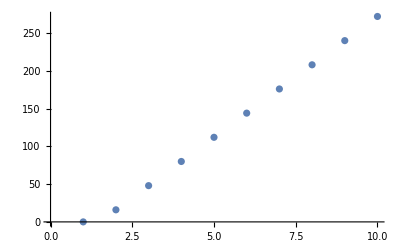

```mathematica
g=GridGraph[{2,4},GraphStyle->"DiagramBlue"];
g
target={{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8}},{{{1,2,3},{2,3,4}},{{2,3,4},{3,4,5}},{{3,4,5},{4,5,6}},{{4,5,6},{5,6,7}},{{5,6,7},{6,7,8}}}};
treeDecomposition[g]==target
checkTreeDecomposition[g,treeDecomposition[g]]
getCost[n_]:=(
g=GridGraph[{2,n},GraphStyle->"DiagramBlue"];
getTreeCost[treeDecomposition[g]]
)
ListPlot[getCost/@Range[10]]
```

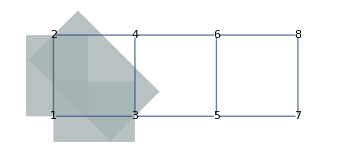
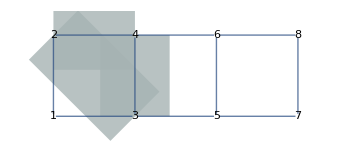
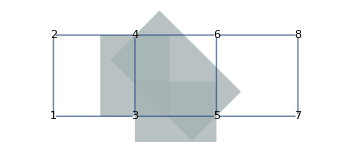
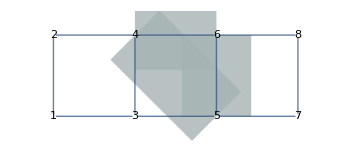
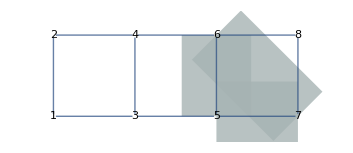
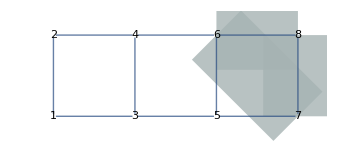

```mathematica
g=GridGraph[{2,4}];
initGraph[g];
drawBagOnGraph/@bags
```